```mathematica
(* Subscript[dx, 1]/dN = f1[x1, x2] and Subscript[dx, 2]/dN = f2[x1, x2] *)
F[x1_,x2_] = Simplify[(1/2-1/(1-x1-x2))(1/(1-x1-x2)-1/2(x1+x2))^-1(3x1+4x2)];
f1[x1_, x2_]:=-x1(F[x1,x2]+3);
f2[x1_, x2_]:=-x2(F[x1,x2]+4);
```

```mathematica
(* compute the fixed points *)
Solve[
{f1[x1,x2] == 0,
f2[x1,x2] == 0},
{x1,x2},
Reals
]
```

{{x1→0,x2→0},{x1→0,x2→1},{x1→1,x2→0}}

```mathematica
(* define the jacobian matrix *)
J[x1_,x2_] = ({{D[f1[x1, x2], x1], D[f1[x1, x2], x2]}, {D[f2[x1, x2], x1], D[f2[x1, x2], x2]}});
```

```mathematica
(* compute the eigenvalues for each fixed point *)
Eigenvalues[J[0,0]]
Eigenvalues[J[0,1]]
Eigenvalues[J[1,0]]
```

{-4,-3}

{4,1}

{3,-1}

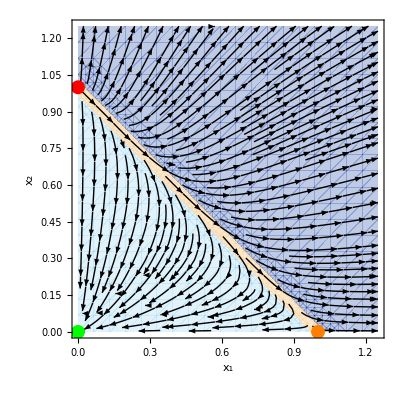

```mathematica
(* show stream plot and all its fixed points *)
(* ver se consigo arranjar forma dele meter os vetores mesmo na linha diagonal para ficar certinho *)
xmax = 1.25;
Show[
RegionPlot[
x1 + x2 <= 0.97, 
{x1, 0, xmax},
{x2, 0 ,xmax}, 
BoundaryStyle->None,
FrameLabel->{Subscript[x, 1], Subscript[x, 2]}, (* tem que ser aqui pq batatas *)
PlotStyle->{RGBColor[137/255,207/255,240/255], Opacity[0.25]}
],
RegionPlot[
0.97<x1 + x2 < 1.0301, 
{x1, 0, xmax},
{x2, 0 ,xmax}, 
BoundaryStyle->None,
PlotStyle->{RGBColor[250/255,214/255,165/255], Opacity[0.5]}
],
RegionPlot[
1.03<=x1 + x2, 
{x1, 0, xmax},
{x2, 0 ,xmax}, 
BoundaryStyle->None,
PlotStyle->{RGBColor[0,45/255,150/255], Opacity[0.25]}
],
StreamPlot[
{f1[x1, x2], f2[x1,x2]},
{x1, 0, xmax},
{x2, 0, xmax},
FrameLabel->{"x_1", "x_2"},
LabelStyle->Bold,
StreamPoints->Fine,
PlotRangePadding -> 0.05,
StreamStyle->Black
],
Graphics[{Green,PointSize -> 0.025,Point[{0,0}]}],
Graphics[{Red,PointSize -> 0.025,Point[{0,1}]}],
Graphics[{Orange,PointSize -> 0.025,Point[{1,0}]}]
]
```

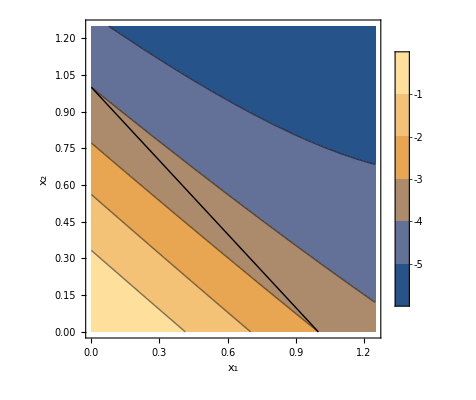

```mathematica
ContourPlot[
F[x1,x2],
{x1,0,1.25},
{x2,0,1.25},
PlotRangePadding -> 0,
FrameLabel -> {"x_1","x_2"},
PlotLegends->Automatic,
Epilog-> Line[{{0,1},{1,0}},VertexColors -> {Black,Black}]
]
```

```mathematica
(* Notas,
- regioes a laranja: x1' < 0 e x2' < 0,
- regiao castanha (-4 < F ≤ -3): x1' ≥ 0 e x2' < 0,- regiao azul: (-5 < F ≤ -4): x1' > 0 e x2' ≥ 0,
*)
```

```mathematica
(* misc - saved for later *)
```

```mathematica
Plot3D[
F[x1,x2],
{x1, 0, 2},
{x2, 0, 2},
PlotRange->{-6, 0},
PlotLegends->Automatic,
PlotRangePadding -> 0,
AxesLabel -> {"x_1","x_2","F(x_1,x_2)"}
]
```

-Graphics3D-